```mathematica
DSolve[ {y'[t]==- b y[t]^3, y[0]== y0},y[t],t]
```

{{y[t]→-1/(√(2 b t+1/y0^2))},{y[t]→1/(√(2 b t+1/y0^2))}}

```mathematica
DSolve[ { x'[t]==a x[t] -b x[t]^3 , x[0]==x0},x[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x[t]→-(√a ⅇ^(a (t+Log[-x0/(√(a-b x0^2))]/a)))/(√(1+b ⅇ^(2 a (t+Log[-x0/(√(a-b x0^2))]/a))))},{x[t]→(√a ⅇ^(a (t+Log[-x0/(√(a-b x0^2))]/a)))/(√(1+b ⅇ^(2 a (t+Log[-x0/(√(a-b x0^2))]/a))))}}

```mathematica
Animate[ Plot[ ( 512/4 )x^4 -   (128/2)x^2 +  8 x Sin[t],{x,-2,2},PlotRange->{{-2,2},{-13,13}}],{t,0,2 π}]
```

```mathematica
f[x_]:= x^4 - x^2  + x Sin[π]
```

```mathematica
f[0.5]
```

-0.1875

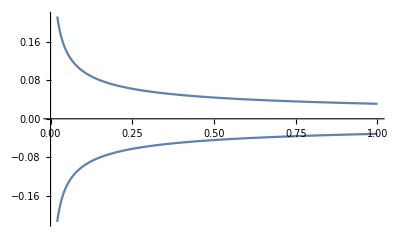

```mathematica
Plot[{-1/(√(2 b t+1/y0^2)) ,1/(√(2 b t+1/y0^2))}/. {b->512, y0->1},{t,0,1}]
```

```mathematica
f = (√a ⅇ^(a (t+Log[-x0/(√(a-b x0^2))]/a)))/(√(1+b ⅇ^(2 a (t+Log[-x0/(√(a-b x0^2))]/a))))
```

(√a ⅇ^(a (t+Log[-x0/(√(a-b x0^2))]/a)))/(√(1+b ⅇ^(2 a (t+Log[-x0/(√(a-b x0^2))]/a))))

```mathematica
f  //Simplify
```

-(√a ⅇ^(a t) x0)/(√(a-b x0^2) √(1+(b ⅇ^(2 a t) x0^2)/(a-b x0^2)))

```mathematica
FindMinimum[( 512/4 )x^4 -   (128/2)x^2 ,{x,1}]
```

{-8.,{x→0.5}}

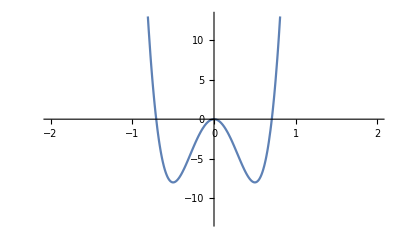

```mathematica
Plot[ ( 512/4 )x^4 -   (128/2)x^2 +  8 x Sin[0],{x,-2,2},PlotRange->{{-2,2},{-13,13}}]
```

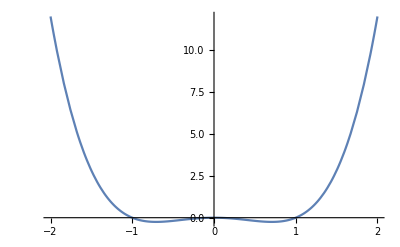

```mathematica
Plot[ ( 1 )x^4 -   (1)x^2 +  1 x Sin[0],{x,-2,2}]
```

```mathematica
FindMinimum[( 1)x^4 -   (1)x^2 ,x]
```

{-0.25,{x→0.707107}}

```mathematica
Sqrt[128/512]
```

1/2

```mathematica
(a^2)/(4  b)   /. a->128 /. b->512
```

8

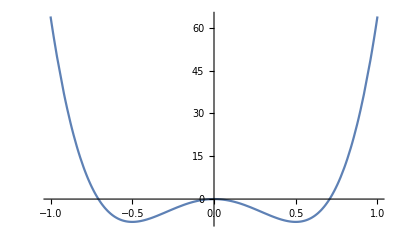

```mathematica
Plot[ ( 512/4 )x^4 -   (128/2)x^2 +  8 x Sin[0],{x,-1,1}]
```